## Constants

```mathematica
C2K[TC_]:=QuantityMagnitude@UnitConvert[Quantity[TC,"DegreesCelsius"],"Kelvins"];
K2C[TK_]:=QuantityMagnitude@UnitConvert[Quantity[TK,"Kelvins"],"DegreesCelsius"];
```

```mathematica
C2F[TC_]:=QuantityMagnitude@UnitConvert[Quantity[TC,"DegreesCelsius"],"DegreesFarenheit"];
F2C[TF_]:=QuantityMagnitude@UnitConvert[Quantity[TF,"DegreesFarenheit"],"DegreesCelsius"];
```

### Unit conversions

```mathematica
bohr2a=QuantityMagnitude@UnitConvert[Quantity[1,"BohrRadius"],"Angstroms"];
a2bohr=1/bohr2a;
au2kcal=QuantityMagnitude[UnitConvert[Quantity[1,"Hartrees"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]];
kcal2au=1/au2kcal;
ev2kcal=QuantityMagnitude[UnitConvert[Quantity[1,"ElectronVolts"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]];
kcal2ev=1/ev2kcal;
ev2cm=QuantityMagnitude@UnitConvert[Quantity[1,"ElectronVolts"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"];
cm2ev=1/ev2cm;
au2ev=QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"],"ElectronVolts"];
ev2au=1/au2ev;
au2cm=QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"];
cm2au=1/au2cm;
au2ps=QuantityMagnitude@UnitConvert[1/(2π)Entity["PhysicalConstant","PlanckConstant"]["Value"],"Hartrees*ps"];
ps2au=1/au2ps;
au2s=au2ps*10^-12;
s2au=1/au2s;
```

### Universal constants

```mathematica
ℏ=1; (* in atomic units *)
hbaraups=1 au2ps; (* in Hartree × ps *)
hbarkcalps=hbaraups au2kcal; (* in kcal/mol × ps *)
Dalton=QuantityMagnitude@UnitConvert[1 Quantity[, "Daltons"],"electronmass"];
μH=QuantityMagnitude@UnitConvert[Quantity[, "ProtonMass"],"electronmass"];
μD=QuantityMagnitude@UnitConvert[Quantity[, "DeuteronMass"],"electronmass"];
MassH=μH/Dalton;
MassD=μD/Dalton;
kbau=QuantityMagnitude@UnitConvert[Entity["PhysicalConstant","BoltzmannConstant"]["Value"],"Hartrees/K"];
kbkcal=kbau au2kcal;
```

## Experimental data (Tafel) for alkaline solution

```mathematica
pH=13;
pD=13.87;
ESDE=-0.013;
ERHE=-0.0591 pH;
ERDeE=ESDE-0.0591pD;
```

### 0.1M KOH in H2O

```mathematica
log10jH={-5.19625,-5.1902,-5.16313,-5.13285,-5.12685,-5.08885,-5.08817,-5.07282,-5.05858,-5.04671,-5.01451,-4.99641,-5.00491,-4.97267,-4.96862,-4.9381,-4.92857,-4.90347,-4.88371,-4.85176,-4.82619,-4.81438,-4.79514,-4.7722,-4.73835,-4.72487,-4.70121,-4.68003,-4.65038,-4.62774,-4.58355,-4.56554,-4.54301,-4.51981,-4.50352,-4.48447,-4.4605,-4.44108,-4.42884,-4.41526,-4.3832,-4.36752,-4.35171,-4.33356,-4.31242,-4.29926,-4.27433,-4.25212,-4.22609,-4.20792,-4.18129,-4.15863,-4.14417,-4.12864,-4.10634,-4.09076,-4.07183,-4.0513,-4.03009,-4.01071,-3.98883,-3.96832,-3.94974,-3.93133,-3.91324,-3.89446,-3.8712,-3.8496,-3.83252,-3.81459,-3.79723,-3.77683,-3.75454,-3.73605,-3.71737,-3.70055,-3.68,-3.65973,-3.64184,-3.62185,-3.60153,-3.58343,-3.56567,-3.54379,-3.52472,-3.50707,-3.48699,-3.46758,-3.44813,-3.42918,-3.41035,-3.39036,-3.37211,-3.35272,-3.33336,-3.31483,-3.29543,-3.27614,-3.2565,-3.23768,-3.21906,-3.20014,-3.18073,-3.16202,-3.14321,-3.12405,-3.10534,-3.08628,-3.06723,-3.04835,-3.02987,-3.01111,-2.9927,-2.97382,-2.95548,-2.93686,-2.91911,-2.90025,-2.88238,-2.86397,-2.84617,-2.82772,-2.80991,-2.79229,-2.77455,-2.75661,-2.73912,-2.7217,-2.70435,-2.68704,-2.66978,-2.65269,-2.63576,-2.61897,-2.6022,-2.58552,-2.5689,-2.5526,-2.53628,-2.52005,-2.50409,-2.48805,-2.47222,-2.4565,-2.4411,-2.42561,-2.41018,-2.39498,-2.37995,-2.36475};
lnjH=log10jH/Log[10,E];
```

```mathematica
ηH={-0.19952,-0.20152,-0.20352,-0.20553,-0.20752,-0.20953,-0.21153,-0.21354,-0.21553,-0.21753,-0.21953,-0.22152,-0.22352,-0.22552,-0.22753,-0.22954,-0.23153,-0.23353,-0.23553,-0.23753,-0.2395,-0.24151,-0.24351,-0.24551,-0.24751,-0.24951,-0.25151,-0.25352,-0.2555,-0.25751,-0.2595,-0.26151,-0.2635,-0.2655,-0.26749,-0.26951,-0.2715,-0.27353,-0.27552,-0.27753,-0.27952,-0.28151,-0.2835,-0.28551,-0.28752,-0.28951,-0.29149,-0.29349,-0.29549,-0.29751,-0.29949,-0.30148,-0.30349,-0.30549,-0.30746,-0.30946,-0.31146,-0.31345,-0.31544,-0.31744,-0.31944,-0.32143,-0.32341,-0.3254,-0.3274,-0.3294,-0.3314,-0.33339,-0.33538,-0.33738,-0.33937,-0.34137,-0.34336,-0.34535,-0.34733,-0.34934,-0.35132,-0.35331,-0.3553,-0.35728,-0.35927,-0.36126,-0.36324,-0.36523,-0.36721,-0.3692,-0.37118,-0.37316,-0.37513,-0.37711,-0.37908,-0.38107,-0.38305,-0.38501,-0.38698,-0.38897,-0.39093,-0.39291,-0.39488,-0.39685,-0.39882,-0.4008,-0.40276,-0.40473,-0.4067,-0.40868,-0.41064,-0.41261,-0.41456,-0.41652,-0.41847,-0.42043,-0.42237,-0.4243,-0.42624,-0.42819,-0.43012,-0.43207,-0.43401,-0.43595,-0.43787,-0.4398,-0.44172,-0.44364,-0.44556,-0.44747,-0.44939,-0.45131,-0.45321,-0.45511,-0.457,-0.4589,-0.4608,-0.46269,-0.46458,-0.46647,-0.46834,-0.47022,-0.47209,-0.47397,-0.47583,-0.4777,-0.47954,-0.4814,-0.48325,-0.48509,-0.48692,-0.48875,-0.49058,-0.49241};
ηHrange=Interval[MinMax[ηH]];
```

```mathematica
ηvslog10jH=Thread[List[log10jH,ηH]];
log10jvsηH=Thread[List[ηH,log10jH]];
lnjvsηH=Thread[List[ηH,lnjH]];
ηvslnjH=Thread[List[lnjH,ηH]];
```

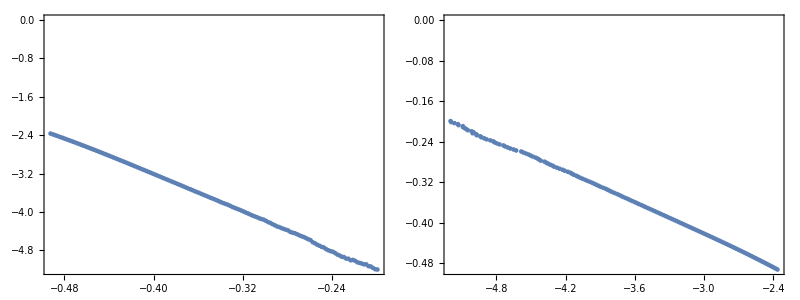

```mathematica
Grid[{
{ListPlot[log10jvsηH,Axes->False,Frame->True,ImageSize->Medium],
ListPlot[ηvslog10jH,Axes->False,Frame->True,ImageSize->Medium]}
}]
```

### 0.1M KOD in D2O

```mathematica
log10jD={-5.84577,-5.80526,-5.74122,-5.72538,-5.72233,-5.69451,-5.64922,-5.63298,-5.60039,-5.5783,-5.53093,-5.50642,-5.51513,-5.48084,-5.46416,-5.46427,-5.45756,-5.44064,-5.43714,-5.38564,-5.37297,-5.36712,-5.32627,-5.31943,-5.30351,-5.25726,-5.25645,-5.22811,-5.21428,-5.18465,-5.1694,-5.16002,-5.13447,-5.111,-5.07293,-5.0447,-5.02954,-5.01735,-4.99687,-4.96832,-4.96815,-4.94465,-4.92842,-4.90549,-4.88765,-4.87235,-4.84668,-4.8181,-4.80335,-4.78732,-4.75568,-4.74356,-4.72179,-4.70289,-4.67763,-4.66569,-4.64843,-4.63055,-4.61452,-4.60514,-4.58532,-4.57396,-4.55963,-4.54576,-4.52998,-4.51267,-4.49702,-4.48078,-4.4695,-4.4526,-4.43716,-4.42851,-4.41408,-4.39438,-4.38027,-4.35922,-4.33602,-4.31951,-4.30239,-4.28176,-4.26686,-4.2549,-4.24447,-4.22987,-4.21279,-4.20139,-4.18585,-4.17142,-4.15763,-4.14039,-4.12457,-4.10831,-4.09077,-4.07828,-4.06308,-4.04942,-4.03464,-4.02426,-4.00873,-3.99306,-3.97521,-3.95992,-3.94382,-3.93122,-3.91772,-3.90411,-3.89166,-3.87642,-3.86035,-3.84595,-3.8323,-3.82008,-3.80712,-3.79262,-3.77591,-3.76035,-3.74917,-3.73694,-3.72304,-3.70795,-3.69339,-3.68065,-3.66847,-3.65512,-3.64019,-3.62671,-3.61465,-3.60215,-3.5874,-3.57476,-3.56255,-3.54907,-3.53509,-3.52392,-3.51185,-3.49828,-3.48588,-3.47473,-3.46068,-3.44851,-3.437,-3.42448,-3.41235,-3.40047,-3.38707,-3.3753,-3.36341,-3.35153,-3.34018,-3.32716,-3.31618,-3.30458,-3.29268,-3.28111,-3.26905,-3.25745,-3.24588,-3.23488,-3.22245,-3.21093,-3.19916,-3.18758,-3.17587,-3.16408,-3.15284,-3.14047,-3.12895};
lnjD=log10jD/Log[10,E];
```

```mathematica
ηD={-0.24956,-0.25358,-0.25557,-0.25756,-0.25956,-0.26957,-0.27157,-0.27359,-0.27558,-0.2776,-0.27959,-0.28159,-0.28358,-0.28558,-0.28758,-0.29156,-0.29357,-0.29757,-0.29955,-0.30356,-0.30557,-0.30756,-0.31156,-0.31555,-0.31755,-0.31955,-0.32155,-0.32354,-0.32554,-0.32954,-0.33153,-0.33353,-0.33553,-0.33754,-0.34352,-0.34551,-0.34751,-0.34951,-0.3515,-0.35349,-0.35548,-0.35747,-0.35946,-0.36147,-0.36345,-0.36546,-0.36744,-0.36944,-0.37143,-0.37343,-0.3754,-0.37739,-0.37938,-0.38137,-0.38336,-0.38533,-0.38732,-0.38931,-0.39129,-0.39329,-0.39527,-0.39727,-0.39925,-0.40125,-0.40324,-0.40522,-0.40721,-0.40921,-0.41119,-0.41318,-0.41517,-0.41716,-0.41914,-0.42112,-0.4231,-0.42507,-0.42705,-0.42903,-0.43101,-0.43297,-0.43494,-0.43694,-0.43892,-0.4409,-0.44286,-0.44484,-0.44681,-0.44879,-0.45076,-0.45271,-0.45469,-0.45666,-0.4586,-0.46058,-0.46255,-0.46451,-0.46646,-0.46844,-0.4704,-0.47236,-0.47431,-0.47626,-0.4782,-0.48017,-0.48211,-0.48407,-0.48603,-0.48797,-0.48991,-0.49184,-0.49378,-0.49573,-0.49768,-0.49961,-0.50154,-0.50344,-0.5054,-0.50734,-0.50925,-0.51117,-0.51308,-0.515,-0.51693,-0.51886,-0.52074,-0.52265,-0.52455,-0.52648,-0.52836,-0.53028,-0.53218,-0.53407,-0.53595,-0.53787,-0.53977,-0.54166,-0.54354,-0.54544,-0.5473,-0.54917,-0.55106,-0.55293,-0.55479,-0.55666,-0.55849,-0.56037,-0.56221,-0.56405,-0.56592,-0.56774,-0.56958,-0.57143,-0.57324,-0.57509,-0.57689,-0.57871,-0.58052,-0.58236,-0.58414,-0.58594,-0.58771,-0.58951,-0.59129,-0.59304,-0.59483,-0.59658,-0.59832};
ηDrange=Interval[MinMax[ηD]];
```

```mathematica
ηvslog10jD=Thread[List[log10jD,ηD]];
log10jvsηD=Thread[List[ηD,log10jD]];
lnjvsηD=Thread[List[ηD,lnjD]];
```

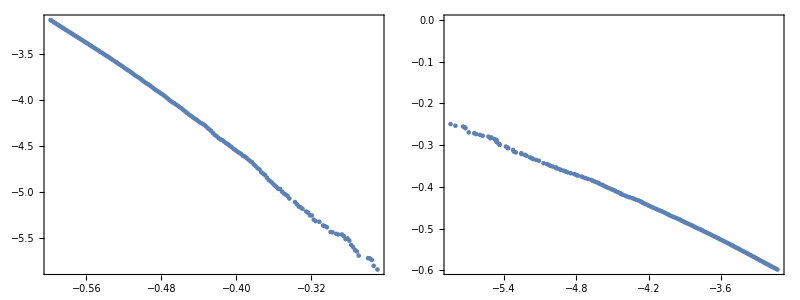

```mathematica
Grid[{
{ListPlot[log10jvsηD,Axes->False,Frame->True,ImageSize->Medium],
ListPlot[ηvslog10jD,Axes->False,Frame->True,ImageSize->Medium]}
}]
```

### Tafel Plots and transfer coefficients

#### Linear fits of the full data for H and D and KIE

```mathematica
lnjvsηHFit=LinearModelFit[lnjvsηH,x,x];
lnjvsηHslope=Normal[lnjvsηHFit]⟦2,1⟧;
αH=-lnjvsηHslope kbau 298.15 au2ev
```

0.58123

```mathematica
lnjvsηDFit=LinearModelFit[lnjvsηD,x,x];
lnjvsηDslope=Normal[lnjvsηDFit]⟦2,1⟧;
αD=-lnjvsηDslope kbau 298.15 au2ev
```

0.461625

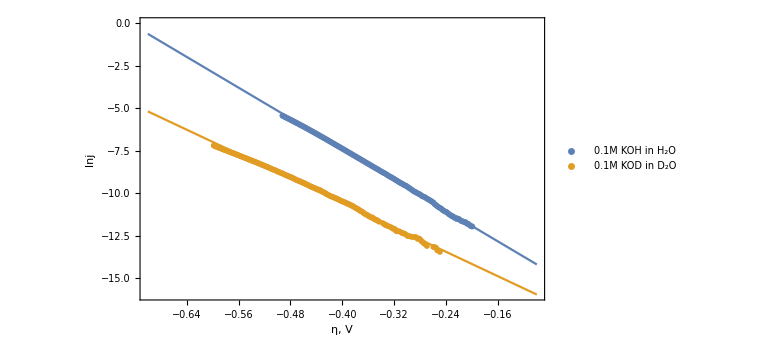

```mathematica
Show[
Plot[{lnjvsηHFit[x],lnjvsηDFit[x]},{x,-0.7,-0.1},
Axes->False,Frame->True,ImageSize->Large],
ListPlot[{lnjvsηH,lnjvsηD},
Axes->False,Frame->True,ImageSize->Large,
PlotLegends->Placed[{"0.1M KOH in H_2O","0.1M KOD in D_2O"},{0.75,0.75}]],
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
FrameLabel->{"η, V","lnj"}
]
```

```mathematica
KIESak[η_]:=Exp[lnjvsηHFit[η]]/Exp[lnjvsηDFit[η]] 10^(pH-pD);
```

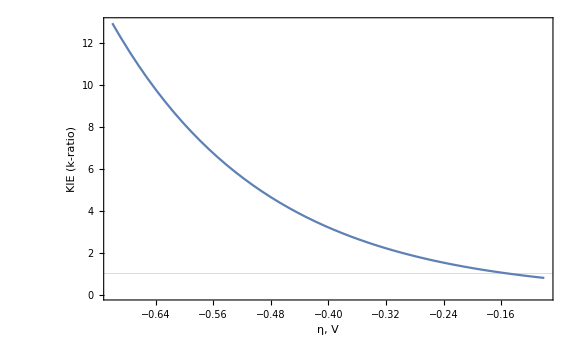

```mathematica
Plot[{KIESak[x]},{x,-0.7,-0.1},
Axes->False,Frame->True,ImageSize->Large,
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
GridLines->{None,{1}},
FrameLabel->{"η, V","KIE (k-ratio)"}]
```

#### Linear fits of the data for overlapping overpotential ranges for H and D and KIE

```mathematica
ηRange=IntervalIntersection[ηHrange,ηDrange]
```

Interval[{-0.49241,-0.24956}]

```mathematica
lnjvsηTruncH=Select[lnjvsηH,IntervalMemberQ[ηRange,#⟦1⟧]&];
lnjvsηTruncD=Select[lnjvsηD,IntervalMemberQ[ηRange,#⟦1⟧]&];
```

```mathematica
lnjvsηTruncHFit=LinearModelFit[lnjvsηTruncH,x,x];
lnjvsηTruncHslope=Normal[lnjvsηTruncHFit]⟦2,1⟧;
αTruncH=-lnjvsηTruncHslope kbau 298 au2ev
```

0.570489

```mathematica
lnjvsηTruncDFit=LinearModelFit[lnjvsηTruncD,x,x];
lnjvsηTruncDslope=Normal[lnjvsηTruncDFit]⟦2,1⟧;
αTruncD=-lnjvsηTruncDslope kbau 298 au2ev
```

0.489097

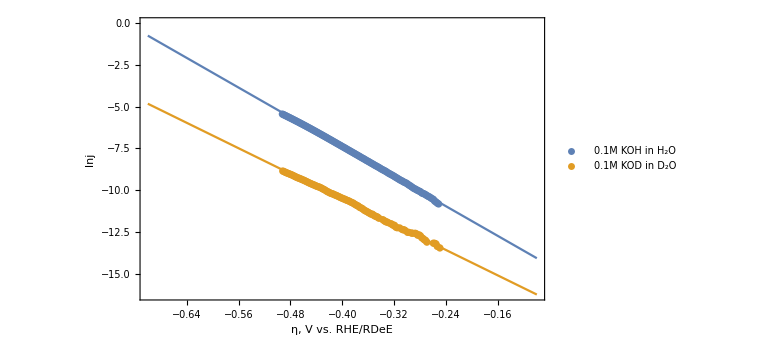

```mathematica
Show[
Plot[{lnjvsηTruncHFit[x],lnjvsηTruncDFit[x]},{x,-0.7,-0.1},
Axes->False,Frame->True,ImageSize->Large],
ListPlot[{lnjvsηTruncH,lnjvsηTruncD},
Axes->False,Frame->True,ImageSize->Large,
PlotLegends->Placed[{"0.1M KOH in H_2O","0.1M KOD in D_2O"},{0.75,0.75}]],
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
FrameLabel->{"η, V vs. RHE/RDeE","lnj"}
]
```

```mathematica
KIETrunc[η_]:=Exp[lnjvsηTruncHFit[η]]/Exp[lnjvsηTruncDFit[η]] 10^(pH-pD);
```

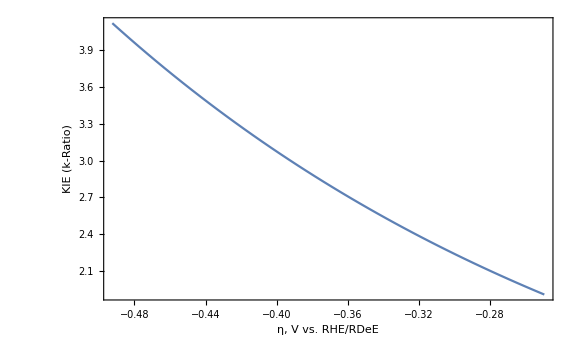

```mathematica
Plot[{KIETrunc[x]},{x,Min[ηRange],Max[ηRange]},
Axes->False,Frame->True,ImageSize->Large,
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
GridLines->{None,{1}},
FrameLabel->{"η, V vs. RHE/RDeE","KIE (k-Ratio)"}]
```

```mathematica
KIEjTrunc[η_]:=Exp[lnjvsηTruncHFit[η]]/Exp[lnjvsηTruncDFit[η]];
```

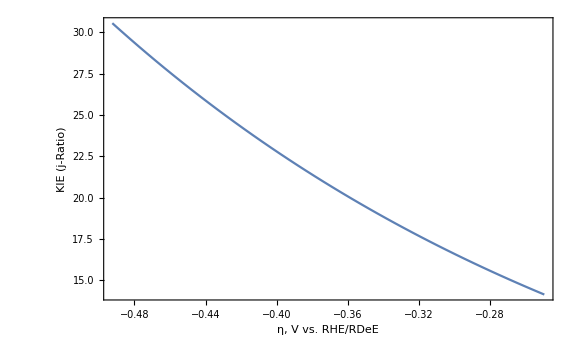

```mathematica
Plot[{KIEjTrunc[x]},{x,Min[ηRange],Max[ηRange]},
Axes->False,Frame->True,ImageSize->Large,
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
GridLines->{None,{1}},
FrameLabel->{"η, V vs. RHE/RDeE","KIE (j-Ratio)"}]
```

## Shift all the data for H and D to the common reference E(SHE)

```mathematica
EH=Map[#+ERHE&,ηH];
Evslog10jH=Thread[List[log10jH,EH]];
log10jvsEH=Thread[List[EH,log10jH]];
lnjvsEH=Thread[List[EH,lnjH]];
EvslnjH=Thread[List[lnjH,EH]];
```

```mathematica
ED=Map[#+ERDeE&,ηD];
Evslog10jD=Thread[List[log10jD,ED]];
log10jvsED=Thread[List[ED,log10jD]];
lnjvsED=Thread[List[ED,lnjD]];
EvslnjD=Thread[List[lnjD,ED]];
```

```mathematica
EHrange=Interval[MinMax[EH]];
EDrange=Interval[MinMax[ED]];
ERange=IntervalIntersection[EHrange,EDrange]
```

Interval[{-1.26071,-1.08228}]

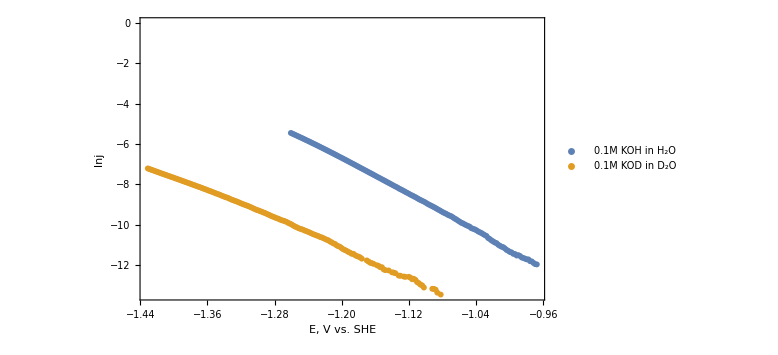

```mathematica
ListPlot[{lnjvsEH,lnjvsED},
Axes->False,Frame->True,ImageSize->Large,
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
FrameLabel->{"E, V vs. SHE","lnj"},
PlotLegends->Placed[{"0.1M KOH in H_2O","0.1M KOD in D_2O"},{0.75,0.75}]]
```

### KIE from linear fits in the full ranges

```mathematica
lnjvsEHFit=LinearModelFit[lnjvsEH,x,x];
lnjvsEHslope=Normal[lnjvsEHFit]⟦2,1⟧;
αEH=-lnjvsEHslope kbau 298.15 au2ev
```

0.58123

```mathematica
lnjvsEDFit=LinearModelFit[lnjvsED,x,x];
lnjvsEDslope=Normal[lnjvsEDFit]⟦2,1⟧;
αED=-lnjvsEDslope kbau 298.15 au2ev
```

0.461625

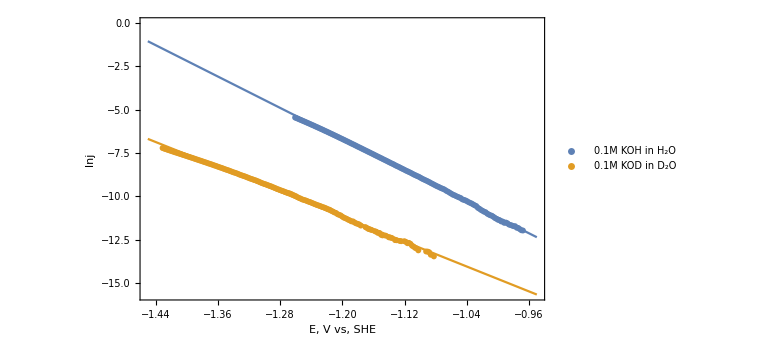

```mathematica
Show[
Plot[{lnjvsEHFit[x],lnjvsEDFit[x]},{x,-1.45,-0.95},
Axes->False,Frame->True,ImageSize->Large],
ListPlot[{lnjvsEH,lnjvsED},
Axes->False,Frame->True,ImageSize->Large,
PlotLegends->Placed[{"0.1M KOH in H_2O","0.1M KOD in D_2O"},{0.75,0.75}]],
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
FrameLabel->{"E, V vs, SHE","lnj"}
]
```

```mathematica
KIESakE[x_]:=Exp[lnjvsEHFit[x]]/Exp[lnjvsEDFit[x]] 10^(pH-pD);
```

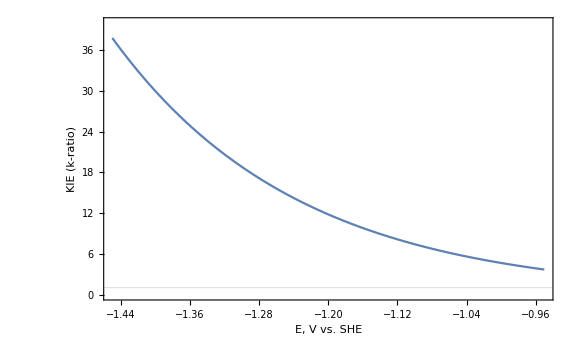

```mathematica
Plot[{KIESakE[x]},{x,-1.45,-0.95},
PlotRange->{0,40},
Axes->False,Frame->True,ImageSize->Large,
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
GridLines->{None,{1}},
FrameLabel->{"E, V vs. SHE","KIE (k-ratio)"}]
```

#### Linear fits of the data for overlapping overpotential ranges for H and D and KIE

```mathematica
lnjvsETruncH=Select[lnjvsEH,IntervalMemberQ[ERange,#⟦1⟧]&];
lnjvsETruncD=Select[lnjvsED,IntervalMemberQ[ERange,#⟦1⟧]&];
```

```mathematica
lnjvsETruncHFit=LinearModelFit[lnjvsETruncH,x,x];
lnjvsETruncHslope=Normal[lnjvsETruncHFit]⟦2,1⟧;
αETruncH=-lnjvsETruncHslope kbau 298 au2ev
```

0.560976

```mathematica
lnjvsETruncDFit=LinearModelFit[lnjvsETruncD,x,x];
lnjvsETruncDslope=Normal[lnjvsETruncDFit]⟦2,1⟧;
αETruncD=-lnjvsETruncDslope kbau 298 au2ev
```

0.49694

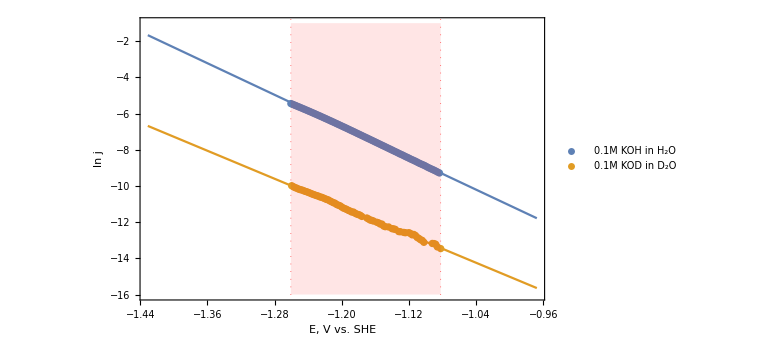

```mathematica
Show[
Plot[{lnjvsETruncHFit[x],lnjvsETruncDFit[x]},{x,Min[EDrange],Max[EHrange]},
PlotRange->{-16,-1},
Axes->False,Frame->True,ImageSize->Large,
GridLines->{{Min[ERange],Max[ERange]},None},
GridLinesStyle->Directive[Red,Dotted]],
ListPlot[{lnjvsETruncH,lnjvsETruncD},
Axes->False,Frame->True,ImageSize->Large,
PlotLegends->Placed[{"0.1M KOH in H_2O","0.1M KOD in D_2O"},{0.55,0.85}]],
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
FrameStyle->Directive[{Black}],
FrameLabel->{"E, V vs. SHE","ln j"},
Epilog->{Red,Opacity[0.1],Rectangle[{Min[ERange],-16},{Max[ERange],-1}]}
]
```

```mathematica
KIETruncE[x_]:=Exp[lnjvsETruncHFit[x]]/Exp[lnjvsETruncDFit[x]] 10^(pH-pD);
```

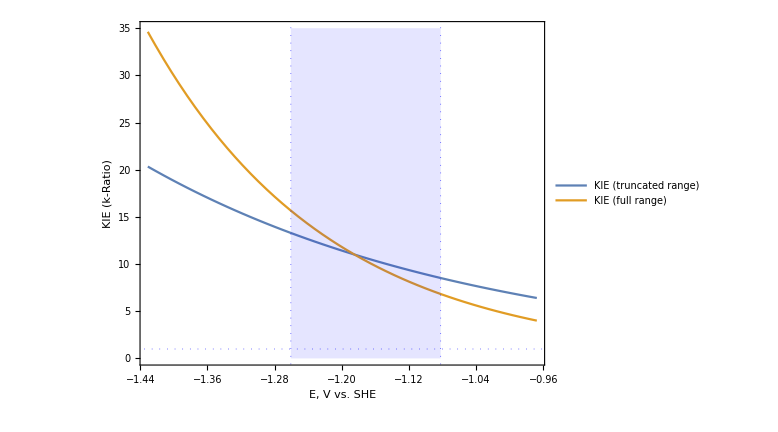

```mathematica
Plot[{KIETruncE[x],KIESakE[x]},{x,Min[EDrange],Max[EHrange]},
PlotRange->{0,35},
Axes->False,Frame->True,ImageSize->Large,AspectRatio->0.75,
FrameStyle->Directive[{Black}],
BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
GridLines->{{Min[ERange],Max[ERange]},{1}},
GridLinesStyle->Directive[Blue,Dotted],
FrameStyle->Black,
FrameLabel->{"E, V vs. SHE","KIE (k-Ratio)"},
PlotLegends->Placed[{Style["KIE (truncated range)",16],Style["KIE (full range)",16]},{0.56,0.85}],
Epilog->{Blue,Opacity[0.1],Rectangle[{Min[ERange],0},{Max[ERange],35}]}
]
```

```mathematica
KIEjTruncE[x_]:=Exp[lnjvsETruncHFit[x]]/Exp[lnjvsETruncDFit[x]];
```

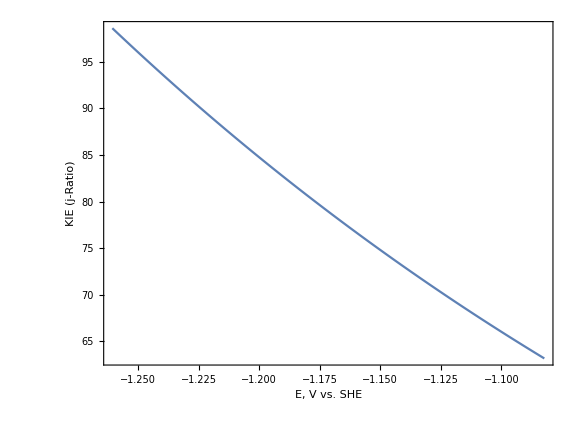

```mathematica
Plot[{KIEjTruncE[x]},{x,Min[ERange],Max[ERange]},
Axes->False,Frame->True,ImageSize->Large,AspectRatio->0.75,
FrameStyle->Directive[{Black}],
BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
GridLines->{None,{1}},
FrameLabel->{"E, V vs. SHE","KIE (j-Ratio)"}]
```